{a→0.202342,c→1.}

Function[r,0.0409425 DiracDelta[r]-Erf[3.4946 r]/r]

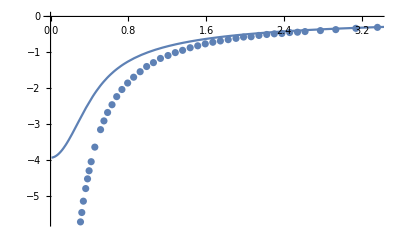

```mathematica
TrueV=Import["C:\\Users\\ASUS\\Documents\\Lepage_TrueV.dat","CSV"];
VeLO=Import["C:\\Users\\ASUS\\Documents\\Lepage_VeLO.dat","CSV"];
(*VeNLO=Import["C:\\Users\\ASUS\\Documents\\Lepage_VeNLO.dat","CSV"];*)
α=1;
ModelVeLO=- α/r Erf[r/(√2 a)]+c a^2 DiracDelta[r];
(*ModelVeNLO=-α/rErf[r/(√2 a)]+c a^2 DiracDelta[r]+d1 a^4 +d2 a^4 Div[DiracDelta[r],{r,θ,ϕ},"Spherical"]Del*)
FitVeLO=FindFit[VeLO,ModelVeLO,{a,c},r]
(*FitVeNLO=FindFit[VeNLO,ModelVeNLO,{a,c,d1,d2},r]*)
VeLOf=Function[r,Evaluate[ModelVeLO/.FitVeLO]]
(*VeNLOf=Function[r,Evaluate[ModelVeNLO/.FitVeNLO]]*)
Show[ListPlot[TrueV],Plot[VeLOf[r],{r,0.01,3.5},Epilog->Map[Point,VeLO]](*,Plot[VeNLOf[r],{r,0.01,3.5},Epilog->Map[Point,VeNLO]]*)]
```